### Load and process data

```mathematica
$HistoryLength=0;
```

```mathematica
importReal64MultiList[dir_,template_]:=Module[{filenameTemplate,depth,dimensions,imported},
filenameTemplate=StringTemplate[template];
depth=StringCount[template,"``"];
dimensions=(Length[FileNames[#,dir,1]]&)@*(TemplateApply[filenameTemplate,Table[If[i==#,"*",0],{i,depth}]]&)/@Range[depth];
imported=Array[Import[dir<>filenameTemplate[##],"Real64"]&,dimensions,ConstantArray[0,depth]];
{dimensions,imported}
];
```

```mathematica
importSetup[paramNames_,paramTypes_,dir_,setupFilename_]:=AssociationThread[paramNames->Import[dir<>setupFilename,"Binary","DataFormat"->paramTypes][[1]]];
```

```mathematica
(*dir=NotebookDirectory[]<>"output/initial_test/";*)
dir="/home/hypermania/Research/BHQuasinormalMode/initial_test/";
paramNames=Import[dir<>"paramNames.txt","List"];
paramTypes=Import[dir<>"paramTypes.txt","List"];
param=importSetup[paramNames,paramTypes,dir,"param.dat"]
```

<|s→2,l→2,r0→1.,r_min→-100.,r_max→100.,N→4096|>

```mathematica
(*{mϕ,v,aKKLT,A,W0,M,ϕi,dtϕi,σi,dtσi,T,tEnd,He,Hinf,logatEnd,σast}=derived=importReal64MultiList[dirBackground,"derived.dat"][[2]];*)
```

```mathematica
rList=Table[param["r_min"]+(param["r_max"]-param["r_min"])/(param["N"]-1)(i-1/2),{i,0,param["N"]}];
```

```mathematica
tList=importReal64MultiList[dir,"t_list.dat"][[2]];
stateList=importReal64MultiList[dir,"state_``.dat"][[2]];
```

```mathematica
ψList=(#[[1;;param[["N"]]+1]]&)/@stateList;
```

```mathematica
Manipulate[ListPlot[{rList,ψList[[i]]}ᵀ,Joined->True,PlotRange->{All,{-0.5,0.5}},ImageSize->Large,AxesLabel->{"r_*","ψ"},Epilog->{Text[Style[StringTemplate["t=``"][tList[[i]]],24],{-50,0.4}]}],{i,1,Length[tList],1}]
```

Part::partd: Part specification $Failed⟦16001⟧ is longer than depth of object.

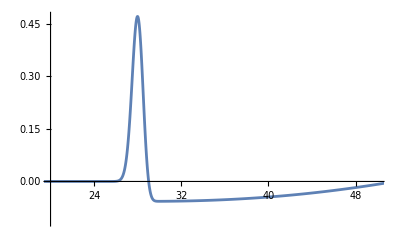

```mathematica
ListPlot[{tList,ψList[[All,2500]]}ᵀ,Joined->True,PlotRange->{{20,50},All}]
```

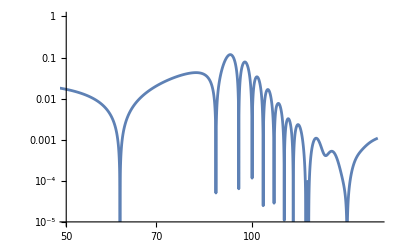

```mathematica
ListLogLogPlot[{tList,ψList[[All,2900]]//Abs}ᵀ,Joined->True,PlotRange->{{50,160},{0.00001,1}}]
```

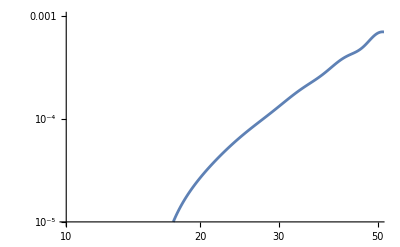

```mathematica
ListLogLogPlot[{rList,ψList[[-1200]]}ᵀ,Joined->True,PlotRange->{{10,50},{10^-5,10^-3}}]
```

### Extracting QNM modes

```mathematica
tToIdx[t_]:=FirstPosition[tList,_?(#>t&)][[1]];
rToIdx[r_]:=FirstPosition[rList,_?(#>r&)][[1]];
```

```mathematica
tFitMin=95;
tFitMax=140;
```

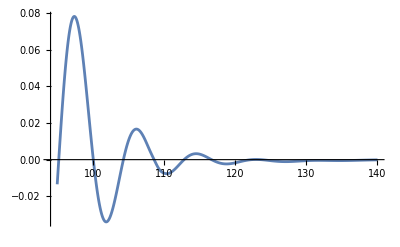

```mathematica
dat={tList,ψList[[All,2900]]}ᵀ[[tToIdx[tFitMin];;tToIdx[tFitMax]]];
ListPlot[dat,Joined->True,PlotRange->{All,All}]
```

```mathematica
(*ListLogPlot[Abs[dat],Joined->True]*)
```

```mathematica
expr=A ⅇ^(-ωI(t-tFitMin))Cos[ωR(t-tFitMin)+θ];
fit=FindFit[dat,{expr,0<A<1,ωI<1,ωI>0,ωR<10,ωR>0,θ>0,θ<2π},{A,ωI,ωR,θ},t,Method->"NMinimize"]
fittedDat=Table[{t,expr}/.fit,{t,tFitMin,tFitMax,0.05}];
```

{A→0.048539,ωI→0.173557,ωR→0.741281,θ→1.50879}

```mathematica
expr2=A1 ⅇ^(-ωI1(t-tFitMin))Cos[ωR1(t-tFitMin)+θ1]+A2 ⅇ^(-ωI2(t-tFitMin))Cos[ωR2(t-tFitMin)+θ2];
fit2=FindFit[dat,{expr2,0<A1<1,0<ωI1<1,0<ωR1<10,0<θ1<2π,0<A2<1,-1<ωI2<1,0<ωR2<10,0<θ2<2π,A1>A2},{A1,ωI1,ωR1,θ1,A2,ωI2,ωR2,θ2},t,Method->"NMinimize"]
```

{A1→0.275808,ωI1→0.277215,ωR1→0.660917,θ1→2.7822,A2→0.145193,ωI2→0.138486,ωR2→0.975518,θ2→6.28319}

```mathematica
fittedDat=Table[{t,expr2}/.fit2,{t,tFitMin,tFitMax,0.1}];
```

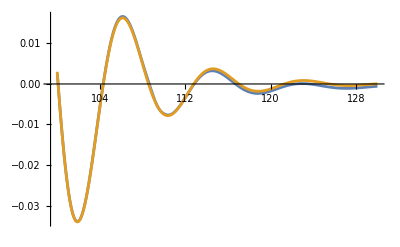

```mathematica
ListLinePlot[{dat,fittedDat},PlotRange->Full]
```

From literature (Spectral decomposition of the perturbation response of the Schwarzschild geometry)

```mathematica
sList={-0.17792-0.74734I,-0.54783-0.69342I,-0.95655-0.60211I,-1.41030 -0.50301I,-1.89369 -0.41503I,-2.39122-0.33860I,-2.89582-0.26650I};
```

```mathematica
BList={0.12690+0.02032I,0.04768-0.22376I,-0.19028+0.01575I,0.08087+0.07961I,-0.01710-0.06053I,-0.00169+0.03643I,0.01067-0.02741I};
```

```mathematica
-ⅈ sList
```

{-0.74734+0.17792 ⅈ,-0.69342+0.54783 ⅈ,-0.60211+0.95655 ⅈ,-0.50301+1.4103 ⅈ,-0.41503+1.89369 ⅈ,-0.3386+2.39122 ⅈ,-0.2665+2.89582 ⅈ}

```mathematica
qnm22Expr=∑_(i=1)^1 BList[[i]]Exp[sList[[i]]t]
```

(0.1269+0.02032 ⅈ) ⅇ^((-0.17792-0.74734 ⅈ) t)

```mathematica
expr=Re[A qnm22Expr]/.t->t-tShift;
fit=FindFit[dat,{expr,tShift>10},{A,tShift},t,Method->"NMinimize"]
fittedDat=Table[{t,expr}/.fit,{t,tFitMin,tFitMax,0.05}];
```

{A→4861.08,tShift→46.9559}

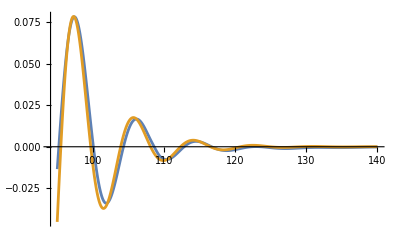

```mathematica
ListLinePlot[{dat,fittedDat},PlotRange->Full,Joined->True]
```

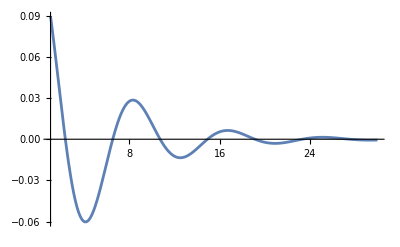

```mathematica
Plot[Re[qnm22Expr],{t,1,30},PlotRange->Full]
```